# Nonstationary simulation, TCA cycle model

```mathematica
<<NilssonLab`MetabolicNetwork`
```

```mathematica
<<NilssonLab`ExtremePathways`
<<NilssonLab`IsotopeDistributions`
<<NilssonLab`AtomMap`
<<NilssonLab`EMUTracing`
```

```mathematica
<<NilssonLab`Visualization`
```

```mathematica
OpenDBConnection[]
```

## Define network model

### Network from database

```mathematica
net=NetworkFromDB["tca-cycle-simple"]
```

<MetabolicNetwork, 19 reactions>

```mathematica
Length[Metabolites[net]]
```

33

Stochiometry matrix (metabolites x reactions) for the reversible network

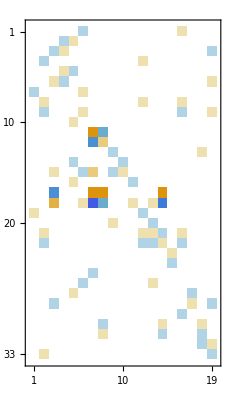

```mathematica
MatrixPlot[Stoichiometry[net]]
```

```mathematica
Union[NonZeroElements[Stoichiometry[net]]]
```

{-8,-5,-4,-2,-1,1,2,3,4}

```mathematica
Table[{ReactionID[r],ReactionFormula[net,r]},{r,Reactions[net]}]//TableForm
```

ACONTm | cit_m <=> icit_m
AKGDm | akg_m + coa_m + nad_m ==> co2_m + nadh_m + succoa_m
ATPS4m | adp_m + 4 h_ims_m + pi_m ==> atp_m + h2o_m + 3 h_m
ATPtm | adp_c + atp_m ==> adp_m + atp_c
CELLWORK | atp_c + h2o_c ==> adp_c + energy_c + h_c + pi_c
CSm | accoa_m + h2o_m + oaa_m ==> cit_m + coa_m + h_m
CYOOm | 4 focytC_m + 8 h_m + o2_m ==> 4 ficytC_m + 2 h2o_m + 4 h_ims_m
CYOR-u10m | 2 ficytC_m + 2 h_m + q10h2_m ==> 2 focytC_m + 4 h_ims_m + q10_m
FUMm | fum_m + h2o_m <=> mal-L_m
H2Otm | h2o_c <=> h2o_m
Htm2 | h_c <=> h_m
ICDHxm | icit_m + nad_m <=> akg_m + co2_m + nadh_m
MDHm | mal-L_m + nad_m <=> h_m + nadh_m + oaa_m
NADH2-u10m | 5 h_m + nadh_m + q10_m ==> 4 h_ims_m + nad_m + q10h2_m
NH4tm | nh4_m <=> nh4_c
PDHm | coa_m + nad_m + pyr_m ==> accoa_m + co2_m + nadh_m
PIt2m | pi_c ==> pi_m
SUCD1m | q10_m + succ_m ==> fum_m + q10h2_m
SUCOASm | adp_m + pi_m + succoa_m ==> atp_m + coa_m + succ_m

```mathematica
Table[{MetaboliteShortName[m],Compartment[m],ExchangeStatus[m]},{m,Metabolites[net]}]//TableForm
```

accoa_m | Mitochondria | Internal
adp_c | Cytosol | Internal
adp_m | Mitochondria | Internal
akg_m | Mitochondria | Uptake
atp_c | Cytosol | Internal
atp_m | Mitochondria | Internal
cit_m | Mitochondria | Internal
co2_m | Mitochondria | Release
coa_m | Mitochondria | Internal
energy_c | Cytosol | Release
ficytC_m | Mitochondria | Internal
focytC_m | Mitochondria | Internal
fum_m | Mitochondria | Internal
h2o_c | Cytosol | Free
h2o_m | Mitochondria | Internal
h_c | Cytosol | Free
h_ims_m | Mitochondria | Internal
h_m | Mitochondria | Internal
icit_m | Mitochondria | Internal
mal-L_m | Mitochondria | Internal
nadh_m | Mitochondria | Internal
nad_m | Mitochondria | Internal
nh4_c | Cytosol | Internal
nh4_m | Mitochondria | Internal
o2_m | Mitochondria | Uptake
oaa_m | Mitochondria | Internal
pi_c | Cytosol | Free
pi_m | Mitochondria | Internal
pyr_m | Mitochondria | Uptake
q10h2_m | Mitochondria | Internal
q10_m | Mitochondria | Internal
succ_m | Mitochondria | Internal
succoa_m | Mitochondria | Internal

#### Generate boundary network

```mathematica
bnet=BoundaryNetwork[net]
```

<BoundaryNetwork, 11 boundary fluxes>

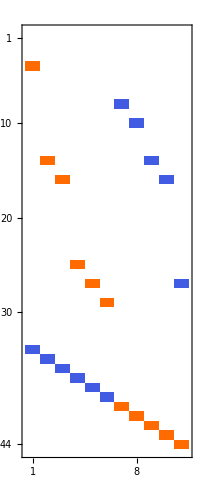

```mathematica
Stoichiometry[bnet]//MatrixPlot
```

```mathematica
BoundaryFluxNames[bnet]
```

{akg_IN,h2o_IN,h_IN,o2_IN,pi_IN,pyr_IN,co2_OUT,energy_OUT,h2o_OUT,h_OUT,pi_OUT}

```mathematica
MetaboliteShortName/@Metabolites[bnet]
```

{accoa_m,adp_c,adp_m,akg_m,atp_c,atp_m,cit_m,co2_m,coa_m,energy_c,ficytC_m,focytC_m,fum_m,h2o_c,h2o_m,h_c,h_ims_m,h_m,icit_m,mal-L_m,nadh_m,nad_m,nh4_c,nh4_m,o2_m,oaa_m,pi_c,pi_m,pyr_m,q10h2_m,q10_m,succ_m,succoa_m,akg_i,h2o_i,h_i,o2_i,pi_i,pyr_i,co2_o,energy_o,h2o_o,h_o,pi_o}

### Extreme points in net flux space

#### Run expa

```mathematica
expa=ExpaExtremePathways[net];
```

```mathematica
Length[expa]
```

8

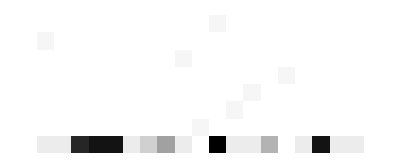

```mathematica
ForwardFlux/@expa//ArrayPlot
```

Random convex combination

```mathematica
RandomFluxVector[corners:{_FluxState..}]:=
Block[{t},
t=RandomReal[UniformDistribution[],Length[corners]];
(t/Total[t]).corners]
```

#### Find viable reactions

Note that this works in the space of net fluxes and hence excludes type III pathways!

```mathematica
netFluxMinMax=FindViableReactions[net];
Dimensions[netFluxMinMax]
```

{19,2}

Convert to absolute flux states and remove duplicates

```mathematica
fluxMinMax=Union[Chop[Join[
Table[FluxState[net,nf],{nf,netFluxMinMax⟦All,1⟧}],
Table[FluxState[net,nf],{nf,netFluxMinMax⟦All,2⟧}]]]];
```

```mathematica
Length[fluxMinMax]
```

2

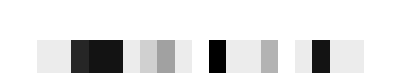

```mathematica
ForwardFlux/@fluxMinMax//ArrayPlot
```

```mathematica
Table[MassBalanceNorm[net,f],{f,fluxMinMax}]//Chop
```

{0,0}

#### Sanity checks

Reactions that cannot carry net flux in the forward direction

```mathematica
Table[
{r,ReactionFormula[net,r]},
{r,Extract[Reactions[net],
Position[Chop[Max/@Transpose[ForwardFlux/@fluxMinMax],0.001],0]]}]//TableForm
```

<Reaction H2Otm(rev)> | h2o_c <=> h2o_m
<Reaction NH4tm(rev)> | nh4_m <=> nh4_c

Reactions that cannot carry net flux in the reverse direction

```mathematica
Table[
{r,ReactionFormula[net,r]},
{r,Extract[Reactions[net],
Intersection[
Position[Chop[Max/@Transpose[ReverseFlux/@fluxMinMax],0.001],0],
Position[ReversibleQ[Reactions[net]],True]]]}]//TableForm
```

<Reaction ACONTm(rev)> | cit_m <=> icit_m
<Reaction FUMm(rev)> | fum_m + h2o_m <=> mal-L_m
<Reaction Htm2(rev)> | h_c <=> h_m
<Reaction ICDHxm(rev)> | icit_m + nad_m <=> akg_m + co2_m + nadh_m
<Reaction MDHm(rev)> | mal-L_m + nad_m <=> h_m + nadh_m + oaa_m
<Reaction NH4tm(rev)> | nh4_m <=> nh4_c

Boundary fluxes that are never non-zero

```mathematica
Pick[InputMetabolites[net],Chop[Max/@Transpose[BoundaryUptake/@fluxMinMax],.01],0]
```

{Metabolite[akg,Input,Boundary],Metabolite[h2o,Input,Boundary],Metabolite[pi,Input,Boundary]}

```mathematica
Pick[OutputMetabolites[net],Chop[Max/@Transpose[BoundaryRelease/@fluxMinMax],0.01],0]
```

{Metabolite[h,Output,Boundary],Metabolite[pi,Output,Boundary]}

### Define true flux vector

#### Random flux vector

```mathematica
randomFlux=RandomFluxVector[fluxMinMax]
```

<FluxState, 19 reactions, 11 b. exch>

```mathematica
TableForm[
Transpose[{ForwardFlux[randomFlux],ReverseFlux[randomFlux]}],
TableHeadings->{Reactions[net],{"Forward","Reverse"}}]
```

| Forward | Reverse
<Reaction ACONTm(rev)> | 65.725 | 0.
<Reaction AKGDm> | 65.725 | 0.
<Reaction ATPS4m> | 755.837 | 0.
<Reaction ATPtm> | 821.562 | 0.
<Reaction CELLWORK> | 821.562 | 0.
<Reaction CSm> | 65.725 | 0.
<Reaction CYOOm> | 164.312 | 0.
<Reaction CYOR-u10m> | 328.625 | 0.
<Reaction FUMm(rev)> | 65.725 | 0.
<Reaction H2Otm(rev)> | 0. | 953.012
<Reaction Htm2(rev)> | 887.287 | 0.
<Reaction ICDHxm(rev)> | 65.725 | 0.
<Reaction MDHm(rev)> | 65.725 | 0.
<Reaction NADH2-u10m> | 262.9 | 0.
<Reaction NH4tm(rev)> | 0. | 0.
<Reaction PDHm> | 65.725 | 0.
<Reaction PIt2m> | 821.562 | 0.
<Reaction SUCD1m> | 65.725 | 0.
<Reaction SUCOASm> | 65.725 | 0.

Total outflow from the system

```mathematica
MassBalance[net,randomFlux]//Chop
```

{0,0,0,0,0,0,0,197.175,0,821.562,0,0,0,131.45,0,-65.725,0,0,0,0,0,0,0,0,-164.312,0,0,0,-65.725,0,0,0,0}

```mathematica
MassBalanceQ[net,randomFlux]
```

True

#### Pyruvate oxidation flux vector

```mathematica
ReactionID/@Reactions[net]
```

{ACONTm,AKGDm,ATPS4m,ATPtm,CELLWORK,CSm,CYOOm,CYOR-u10m,FUMm,H2Otm,Htm2,ICDHxm,MDHm,NADH2-u10m,NH4tm,PDHm,PIt2m,SUCD1m,SUCOASm}

```mathematica
fluxRules={"ACONTm"->{1,0},"AKGDm"->{1,0},"ATPS4m"->{11.5,0},"ATPtm"->{12.5,0},"CELLWORK"->{12.5,0},"CSm"->{1,0},"CYOOm"->{2.5,0},"CYOR-u10m"->{5,0},"FUMm"->{1,0},"H2Otm"->{0,14.5},"Htm2"->{13.5,0},"ICDHxm"->{1,0},"MDHm"->{1,0},"NADH2-u10m"->{4,0},"NH4tm"->{1,1},"PDHm"->{1,0},"PIt2m"->{12.5,0},"SUCD1m"->{1,0},"SUCOASm"->{1,0}};
```

NOTE: here we must add a small constant to avoid zero throughput fluxes, which messes up the steady state simulation

```mathematica
fluxEpsilon=10^(-6);
```

```mathematica
pyrOxFlux=FluxState[net,Sequence@@Transpose[(ReactionID/@Reactions[net])/.fluxRules]]
```

<FluxState, 19 reactions, 11 b. exch>

Nonzero metabolite balances

```mathematica
Block[{bal,mi},
bal=MassBalance[net,pyrOxFlux];
mi=Flatten[Position[Chop[bal],Except[0],Heads->False]];
TableForm[bal⟦mi⟧,TableHeadings->{Metabolites[net]⟦mi⟧,None}]]
```

Metabolite[co2,Mitochondria,Release] | 3.
Metabolite[energy,Cytosol,Release] | 12.5
Metabolite[h2o,Cytosol,Free] | 2.
Metabolite[h,Cytosol,Free] | -1.
Metabolite[o2,Mitochondria,Uptake] | -2.5
Metabolite[pyr,Mitochondria,Uptake] | -1.

```mathematica
TableForm[
Transpose[{ForwardFlux[pyrOxFlux],ReverseFlux[pyrOxFlux]}],
TableHeadings->{Reactions[net],{"Forward","Reverse"}}]
```

| Forward | Reverse
<Reaction ACONTm(rev)> | 1 | 0
<Reaction AKGDm> | 1 | 0
<Reaction ATPS4m> | 11.5 | 0
<Reaction ATPtm> | 12.5 | 0
<Reaction CELLWORK> | 12.5 | 0
<Reaction CSm> | 1 | 0
<Reaction CYOOm> | 2.5 | 0
<Reaction CYOR-u10m> | 5 | 0
<Reaction FUMm(rev)> | 1 | 0
<Reaction H2Otm(rev)> | 0 | 14.5
<Reaction Htm2(rev)> | 13.5 | 0
<Reaction ICDHxm(rev)> | 1 | 0
<Reaction MDHm(rev)> | 1 | 0
<Reaction NADH2-u10m> | 4 | 0
<Reaction NH4tm(rev)> | 1 | 1
<Reaction PDHm> | 1 | 0
<Reaction PIt2m> | 12.5 | 0
<Reaction SUCD1m> | 1 | 0
<Reaction SUCOASm> | 1 | 0

```mathematica
MassBalanceQ[net,pyrOxFlux]
```

True

#### Choose a vector

```mathematica
trueFlux=pyrOxFlux;
```

## Atom map

### Define atom map

All atom transitions for reactions in model

```mathematica
atomMap=RemoveUnreachable[net,AtomMapsFromDB[net,{"C"}]]
```

{<AtomMap, 6 transitions>,<AtomMap, 5 transitions>,<AtomMap, 0 transitions>,<AtomMap, 0 transitions>,<AtomMap, 0 transitions>,<AtomMap, 6 transitions>,<AtomMap, 0 transitions>,<AtomMap, 0 transitions>,<AtomMap, 4 transitions>,<AtomMap, 0 transitions>,<AtomMap, 0 transitions>,<AtomMap, 6 transitions>,<AtomMap, 4 transitions>,<AtomMap, 0 transitions>,<AtomMap, 0 transitions>,<AtomMap, 3 transitions>,<AtomMap, 0 transitions>,<AtomMap, 4 transitions>,<AtomMap, 4 transitions>}

Renumber for use with INCA

```mathematica
atomMap=RenumberAtoms[atomMap];
```

Consistency check, ensure that there are no broken paths on the atom level

```mathematica
CheckAtomMap[atomMap]
```

{}

```mathematica
AtomList[atomMap]//Length
```

43

```mathematica
Total[Length/@EductList/@atomMap]
```

42

Reactions with no atom mappings.

```mathematica
Pick[Reactions[net],EductArity/@atomMap,0]
```

{<Reaction ATPS4m>,<Reaction ATPtm>,<Reaction CELLWORK>,<Reaction CYOOm>,<Reaction CYOR-u10m>,<Reaction H2Otm(rev)>,<Reaction Htm2(rev)>,<Reaction NADH2-u10m>,<Reaction NH4tm(rev)>,<Reaction PIt2m>}

Metabolites without any atoms mapped

```mathematica
MetaboliteShortName/@Complement[Metabolites[net],Metabolite/@AtomList[atomMap]]//Sort
```

{adp_c,adp_m,atp_c,atp_m,coa_m,energy_c,ficytC_m,focytC_m,h2o_c,h2o_m,h_c,h_ims_m,h_m,nadh_m,nad_m,nh4_c,nh4_m,o2_m,pi_c,pi_m,q10h2_m,q10_m}

Cretate boundary atom maps (uptake / release)

```mathematica
bmap=BoundaryAtomMaps[net,atomMap];
bmap//Length
```

11

```mathematica
Reactions[net]⟦13⟧
```

<Reaction MDHm(rev)>

```mathematica
atomMap⟦13⟧//InputForm
```

AtomMap[{{Atom[Metabolite["mal-L", "Mitochondria", "Internal"], "C", 1], 1}, {Atom[Metabolite["mal-L", "Mitochondria", "Internal"], "C", 2], 
   1}, {Atom[Metabolite["mal-L", "Mitochondria", "Internal"], "C", 3], 1}, {Atom[Metabolite["mal-L", "Mitochondria", "Internal"], "C", 4], 
   1}}, {{Atom[Metabolite["oaa", "Mitochondria", "Internal"], "C", 1], 1}, {Atom[Metabolite["oaa", "Mitochondria", "Internal"], "C", 2], 1}, 
  {Atom[Metabolite["oaa", "Mitochondria", "Internal"], "C", 3], 1}, {Atom[Metabolite["oaa", "Mitochondria", "Internal"], "C", 4], 1}}]

### Symmetry

```mathematica
symmetry=GetSymmetryMap[atomMap]
```

{fum→{{1,2},{3,4}},succ→{{1,2},{3,4}}}

### Visualizations

Matrix of connections between atoms

```mathematica
AtomToAtomAdjacencyMatrix[net,atomMap]//ArrayPlot
```

-Graphics-

Complete graph

```mathematica
AdjacencyGraph[AtomList[atomMap],AtomToAtomAdjacencyMatrix[net,atomMap]]
```

-Graphics-

Subgraphs for connected components

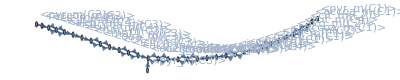
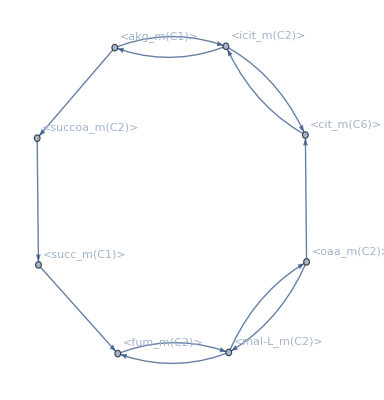

```mathematica
Block[{A,cl},
A=AdjacencyGraph[AtomList[atomMap],AtomToAtomAdjacencyMatrix[net,atomMap]];
cl=Cases[WeaklyConnectedComponents[A],c_List/;Length[c]>1];
Table[
Subgraph[A,c,VertexLabels->"Name"],
{c,cl}]]
```

## Specify input isotopomers (tracers)

```mathematica
<<NilssonLab`IsotopeDistributions`
```

Isotopomer distributions for substrates (tracers), one entry for each experiment

```mathematica
substrates=Cases[MetaboliteEMUs[bmap],EMU[Metabolite[_,"Input",_],__]]
```

{<akg_i{(12345)}>,<pyr_i{(123)}>}

Specify fraction labeled pyruvate

```mathematica
substrateDist=With[{p=1.0},
substrates/.{
e:EMU[m:Metabolite["pyr",__],__]:>
Rule[m,EmpiricalIsotopomerDistribution[{{{Table[1,EMUSize[e]]},p},{{Table[0,EMUSize[e]]},1-p}}]],
e:EMU[met_Metabolite,__]:>Rule[met,EmpiricalIsotopomerDistribution[{{{Table[0,EMUSize[e]]},1.0}}]]}]
```

{Metabolite[akg,Input,Boundary]→EmpiricalIsotopomerDistribution[{{{{0,0,0,0,0}},1.}}],Metabolite[pyr,Input,Boundary]→EmpiricalIsotopomerDistribution[{{{{1,1,1}},1.},{{{0,0,0}},0.}}]}

## Generate EMU model

The EMU system is the same for stationary (steady-state) and nonstationary analysis.

We generate a carbon-only EMU network by specifying only carbon fragments as targets

```mathematica
targets=MetaboliteEMUs[atomMap]
```

{<accoa_m{(12)}>,<akg_m{(12345)}>,<cit_m{(123456)}>,<co2_m{(1)}>,<fum_m{(1234)}>,<icit_m{(123456)}>,<mal-L_m{(1234)}>,<oaa_m{(1234)}>,<pyr_m{(123)}>,<succ_m{(1234)}>,<succoa_m{(1234)}>}

### EMU decomposition

This generates a set of EMU reactions. No symmetry in this case

```mathematica
emuReactions=EMUAlgorithm[net,atomMap,bmap,{"C"},targets,symmetry];
Length[emuReactions]
```

132

For a specific product

```mathematica
Cases[emuReactions,EMUReaction[_,_,EMU[Metabolite["succ",__],{{{1}}}],__]]//TableForm
```

{}

```mathematica
Cases[emuReactions,EMUReaction[_,_,EMU[Metabolite["cit","Mitochondria",_],__],__]]//TableForm
```

EMUReaction[12,<accoa_m{(12)} x oaa_m{(1234)}>,<cit_m{(123456)}>,1]
EMUReaction[26,<icit_m{(123456)}>,<cit_m{(123456)}>,1]
EMUReaction[12,<oaa_m{(4)}>,<cit_m{(5)}>,1]
EMUReaction[26,<icit_m{(5)}>,<cit_m{(5)}>,1]
EMUReaction[12,<accoa_m{(12)} x oaa_m{(123)}>,<cit_m{(12346)}>,1]
EMUReaction[26,<icit_m{(12346)}>,<cit_m{(12346)}>,1]
EMUReaction[12,<oaa_m{(3)}>,<cit_m{(3)}>,1]
EMUReaction[26,<icit_m{(3)}>,<cit_m{(3)}>,1]
EMUReaction[12,<accoa_m{(12)} x oaa_m{(12)}>,<cit_m{(1246)}>,1]
EMUReaction[26,<icit_m{(1246)}>,<cit_m{(1246)}>,1]
EMUReaction[12,<oaa_m{(1)}>,<cit_m{(1)}>,1]
EMUReaction[26,<icit_m{(1)}>,<cit_m{(1)}>,1]
EMUReaction[12,<accoa_m{(2)}>,<cit_m{(4)}>,1]
EMUReaction[26,<icit_m{(6)}>,<cit_m{(4)}>,1]
EMUReaction[12,<accoa_m{(1)} x oaa_m{(12)}>,<cit_m{(126)}>,1]
EMUReaction[26,<icit_m{(124)}>,<cit_m{(126)}>,1]
EMUReaction[12,<accoa_m{(12)} x oaa_m{(2)}>,<cit_m{(246)}>,1]
EMUReaction[26,<icit_m{(246)}>,<cit_m{(246)}>,1]
EMUReaction[12,<accoa_m{(1)} x oaa_m{(2)}>,<cit_m{(26)}>,1]
EMUReaction[26,<icit_m{(24)}>,<cit_m{(26)}>,1]
EMUReaction[12,<accoa_m{(1)}>,<cit_m{(2)}>,1]
EMUReaction[26,<icit_m{(4)}>,<cit_m{(2)}>,1]
EMUReaction[12,<oaa_m{(2)}>,<cit_m{(6)}>,1]
EMUReaction[26,<icit_m{(2)}>,<cit_m{(6)}>,1]

Number of EMUs

```mathematica
emus=Union[Cases[emuReactions,EMUReaction[_,_,e_EMU,_]->e]];
emus//Length
```

77

Generate equation systems

```mathematica
emuEq=EMUSystem[emuReactions,NumberOfFluxes[EMUFluxMap[net]]];
```

```mathematica
TableForm[emuEq,TableHeadings->Automatic]
```

1 | <EMUEquation (1), 39 internals, 8 substrates, 0 condensations >
2 | <EMUEquation (2), 10 internals, 2 substrates, 1 condensations >
3 | <EMUEquation (3), 15 internals, 3 substrates, 2 condensations >
4 | <EMUEquation (4), 8 internals, 1 substrates, 1 condensations >
5 | <EMUEquation (5), 3 internals, 1 substrates, 1 condensations >
6 | <EMUEquation (6), 2 internals, 0 substrates, 2 condensations >

Total number of isotopomer variables in the equation system

```mathematica
Total[Map[(Times@@#&),(Dimensions/@emus)+1]]
```

240

### Substrate EMUs

Calculate MIDs for network substrate EMUs

```mathematica
EMUMassIsotopomerDistribution[e_EMU,isoDist_]:=
Block[{a,ml},
(* arbitrarily pick first member of equiv. class *)
a=First[AtomNumbers[e]];
(* list of masses of the EMU *)
ml=Tuples[Map[Range[0,Length[#]]&,a]];
Table[
PDF[MarginalizeToMID[FragmentIsotopomerDistribution[isoDist,a]],x],
{x,ml}]]
```

```mathematica
irList={Table[
Rule[e,EMUMassIsotopomerDistribution[e,Metabolite[e]/.substrateDist]],
{e,Flatten[SubstrateEMUs/@emuEq]}]}
```

{{<akg_i{(1)}>→{1.,0.},<akg_i{(2)}>→{1.,0.},<akg_i{(3)}>→{1.,0.},<akg_i{(4)}>→{1.,0.},<akg_i{(5)}>→{1.,0.},<pyr_i{(1)}>→{0.,1.},<pyr_i{(2)}>→{0.,1.},<pyr_i{(3)}>→{0.,1.},<akg_i{(12)}>→{1.,0.,0.},<pyr_i{(12)}>→{0.,0.,1.},<akg_i{(123)}>→{1.,0.,0.,0.},<akg_i{(124)}>→{1.,0.,0.,0.},<pyr_i{(123)}>→{0.,0.,0.,1.},<akg_i{(1234)}>→{1.,0.,0.,0.,0.},<akg_i{(12345)}>→{1.,0.,0.,0.,0.,0.}}}

## Simulate steady-state mass isotopomer data

```mathematica
<<NilssonLab`EMUTracing`
```

```mathematica
TableForm[
Round[EMUFluxMap[net][trueFlux],0.01],
TableHeadings->{EMUFluxMap[net,"reactions"],None}]
```

akg_IN | 0.
h2o_IN | 0.
h_IN | 1.
o2_IN | 2.5
pi_IN | 0.
pyr_IN | 1.
ACONTm_f | 1.
AKGDm_f | 1.
ATPS4m_f | 11.5
ATPtm_f | 12.5
CELLWORK_f | 12.5
CSm_f | 1.
CYOOm_f | 2.5
CYOR-u10m_f | 5.
FUMm_f | 1.
H2Otm_f | 0.
Htm2_f | 13.5
ICDHxm_f | 1.
MDHm_f | 1.
NADH2-u10m_f | 4.
NH4tm_f | 1.
PDHm_f | 1.
PIt2m_f | 12.5
SUCD1m_f | 1.
SUCOASm_f | 1.
ACONTm_r | 0.
FUMm_r | 0.
H2Otm_r | 14.5
Htm2_r | 0.
ICDHxm_r | 0.
MDHm_r | 0.
NH4tm_r | 1.

```mathematica
emuSol=EMUSimulate[emuEq,irList⟦1⟧,EMUFluxMap[net][trueFlux]]
```

<EMUSolution, 6 subsystems>

```mathematica
TableForm[emuSol/@targets,TableHeadings->{targets,None}]
```

<accoa_m{(12)}> | 0. | 0. | 1. |  |  |  | 
<akg_m{(12345)}> | 0. | 0. | 0. | 0. | 0. | 1. | 
<cit_m{(123456)}> | 0. | 0. | 0. | 0. | 0. | 0. | 1.
<co2_m{(1)}> | 0. | 1. |  |  |  |  | 
<fum_m{(1234)}> | 0. | 0. | 0. | 0. | 1. |  | 
<icit_m{(123456)}> | 0. | 0. | 0. | 0. | 0. | 0. | 1.
<mal-L_m{(1234)}> | 0. | 0. | 0. | 0. | 1. |  | 
<oaa_m{(1234)}> | 0. | 0. | 0. | 0. | 1. |  | 
<pyr_m{(123)}> | 0. | 0. | 0. | 1. |  |  | 
<succ_m{(1234)}> | 0. | 0. | 0. | 0. | 1. |  | 
<succoa_m{(1234)}> | 0. | 0. | 0. | 0. | 1. |  |

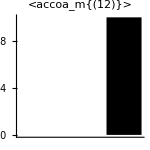
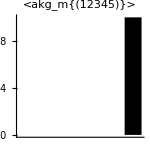
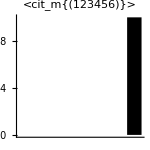
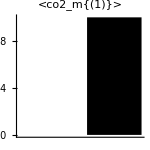
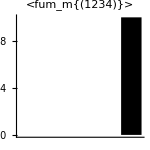
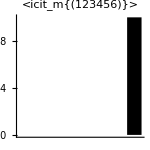
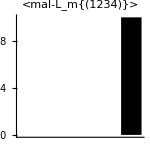
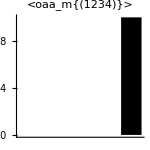

```mathematica
Table[
SimpleBarChart[emuSol[e],PlotLabel->e,AspectRatio->1,ImageSize->150],
{e,targets}]
```

## Nonstationary simulation

```mathematica
<<NilssonLab`EMUTracing`
```

Here, all MI fractions are time-dependent variables, and each internal EMU is associate with a differential equation over time rather than an algebraic equation. The condensations are the same, but also time dependent.

In tensor form, the steady state equation is A v X + B v Y + C v Z - D v X = 0  <--> (A-D) v X = - B v Y - C v Z
The nonstationary version is 
T * dX/dt = A v X(t) + B b Y + C v Z(t) - D v X(t)
where T is a diagnonal matrix of concentrations for each metabolite (same for all EMUs from that metabolite)

### Generate EMU diff equations

Define concentrations for each metabolite

Lower concentration for “tracer” accoa to reflect rapid accumulation?

```mathematica
(*metaboliteConc={Metabolite["accoa",_,_]->0.01,_Metabolite->1.0};*)
```

```mathematica
metaboliteConc=Thread[Metabolites[net]->1.0];
```

```mathematica
emuDiffEqn=EMUDiffEquation[emuEq,x,t,irList⟦1⟧,EMUFluxMap[net][trueFlux],Map[Metabolite,InternalEMUs/@emuEq,{2}]/.metaboliteConc];
```

```mathematica
Dimensions/@emuDiffEqn
```

{{39,2},{10,3},{15,4},{8,5},{3,6},{2,7}}

```mathematica
Length[Flatten[emuDiffEqn]]
```

240

### Simulate system

```mathematica
variables=Table[
x[e,j],
{eq,emuEq},{e,InternalEMUs[eq]},{j,0,EMUSize[First[InternalEMUs[eq]]]}];
```

```mathematica
Dimensions/@variables
```

{{39,2},{10,3},{15,4},{8,5},{3,6},{2,7}}

We will need an initial MID state. Here we take the unlabeled state, so that x[e, j] is the unit vector

```mathematica
initial=Table[
x[e,j][0]==If[j==0,1,0],
{eq,emuEq},{e,InternalEMUs[eq]},{j,0,EMUSize[First[InternalEMUs[eq]]]}];
```

```mathematica
Dimensions/@initial
```

{{39,2},{10,3},{15,4},{8,5},{3,6},{2,7}}

Simulation with NDSolve

```mathematica
tFinal=50.0;
```

```mathematica
sol=variables/.First[NDSolve[
Join[Flatten[emuDiffEqn],Flatten[initial]],
Flatten[variables],{t,0,tFinal}]];//AbsoluteTiming
```

{0.0466947,Null}

```mathematica
Dimensions/@sol
```

{{39,2},{10,3},{15,4},{8,5},{3,6},{2,7}}

EMU variables per metabolite

```mathematica
Table[Count[Flatten[variables],x[EMU[m,__],_]],{m,Metabolites[net]}]
```

{7,0,0,32,0,0,41,2,0,0,0,0,16,0,0,0,0,0,41,24,0,0,0,0,0,24,0,0,13,0,0,16,24}

### All solutions

```mathematica
(*Plot[Table[f[t],{f,Flatten[sol]}],{t,0,2}]*)
```

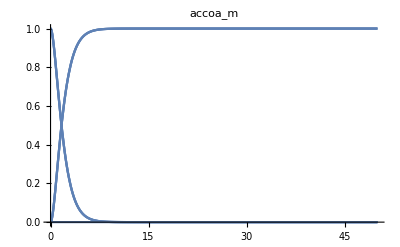
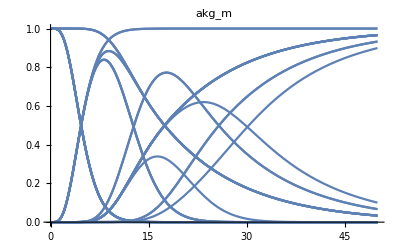
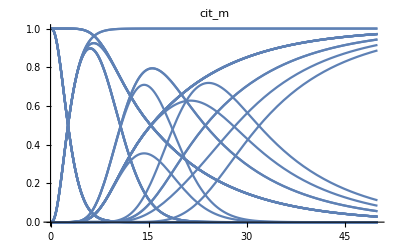
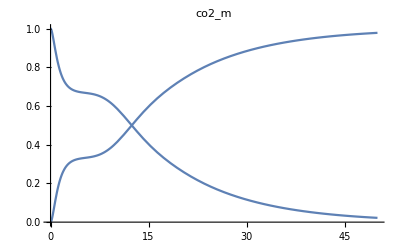
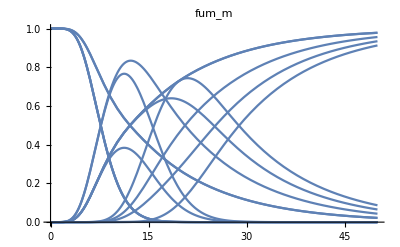
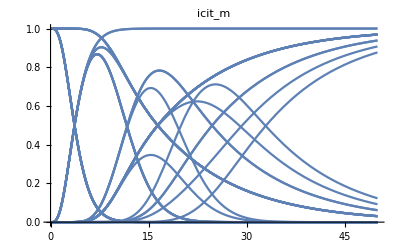
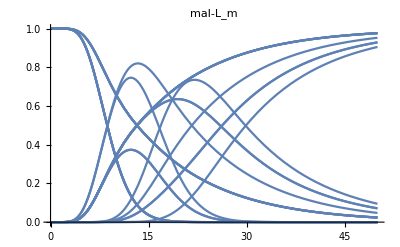
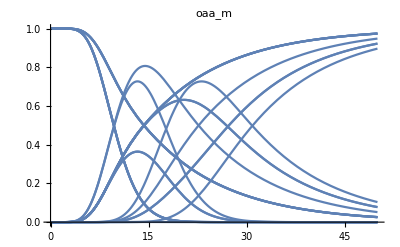

```mathematica
Block[{fl},
Table[
fl=Extract[sol,Position[variables,x[EMU[m,__],_]]];
If[Length[fl]>0,
Plot[Table[f[t],{f,Flatten[fl]}],{t,0,tFinal},PlotLabel->MetaboliteShortName[m]],
{}],
{m,Metabolites[net]}]]//Flatten
```

Without symmetry

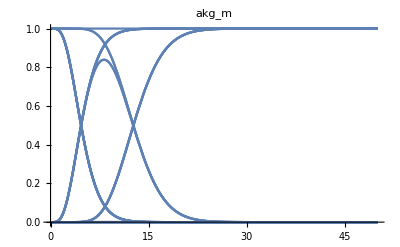
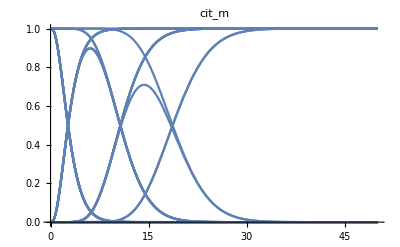
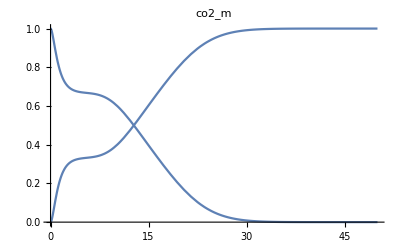
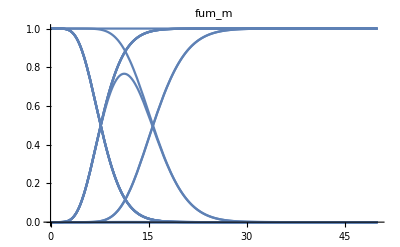
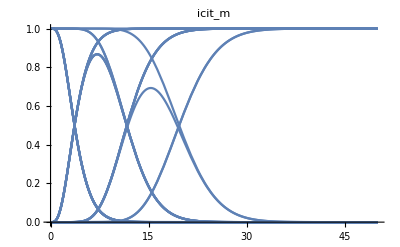
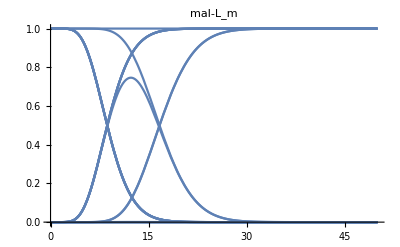
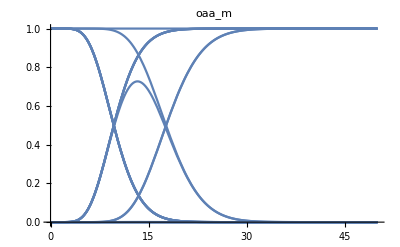
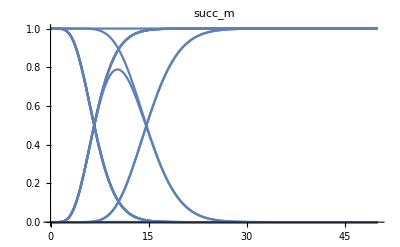
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

### All targets

```mathematica
(*Plot[Table[f[t],{f,Flatten[sol]}],{t,0,2}]*)
```

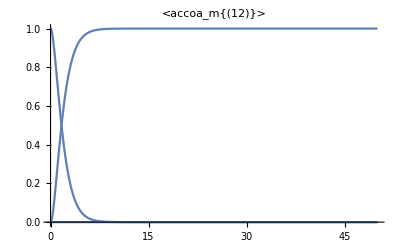
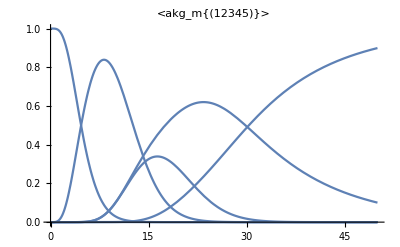
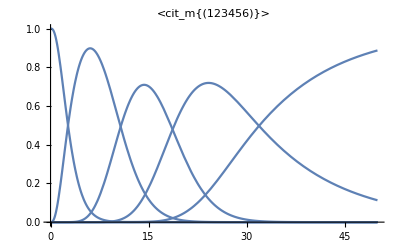
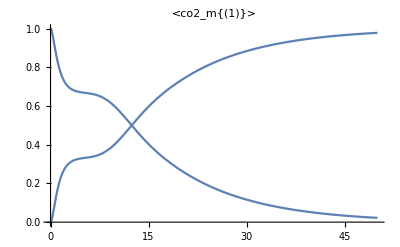
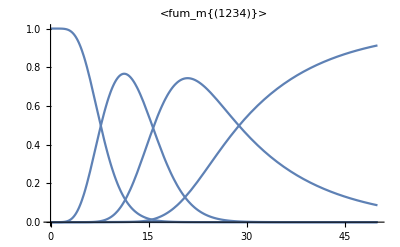
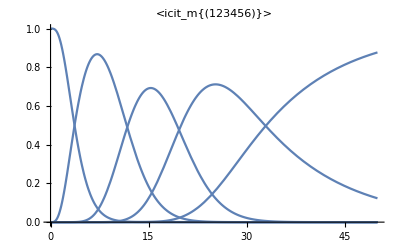
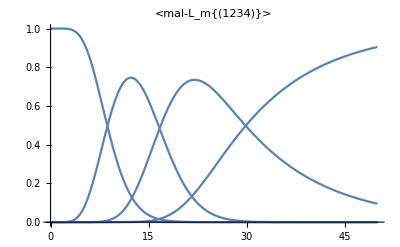
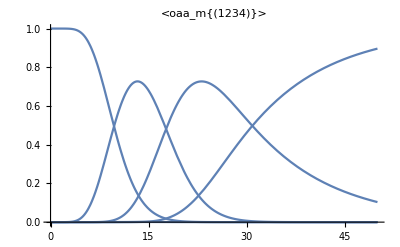

```mathematica
Block[{fl},
Table[
fl=Extract[sol,Position[variables,x[emu,_]]];
Plot[Table[f[t],{f,Flatten[fl]}],{t,0,tFinal},PlotLabel->emu],
{emu,targets}]]//Flatten
```

### Fully labeled MIs

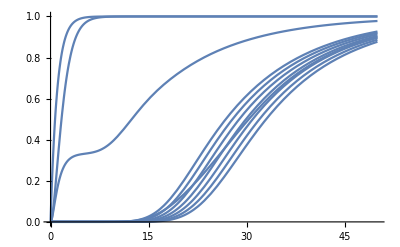

```mathematica
Block[{ix,functions,vars},
ix=Position[
variables,
Alternatives@@Table[x[emu,EMUSize[emu]],{emu,targets}]];
functions=Extract[sol,ix];
vars=Extract[variables,ix];
Plot[
Table[functions⟦i⟧[t],{i,Length[vars]}],
{t,0,tFinal},PlotLegends->Automatic]]
```

### Specific metabolites

#### Citrate

All EMUs

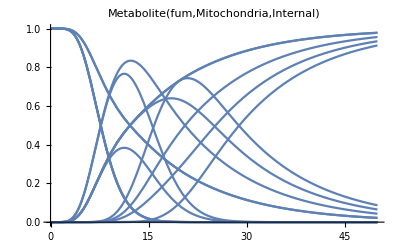

```mathematica
Block[{fl,m=Metabolites[net]⟦13⟧},
fl=Extract[sol,Position[variables,x[EMU[m,__],_]]];
Plot[Table[f[t],{f,Flatten[fl]}],{t,0,tFinal},PlotLabel->m]]
```

Metabolite EMUs (mass isotopomers)

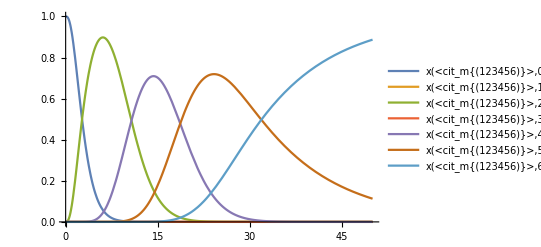

```mathematica
Block[{ix,fl,vl},
ix=Position[variables,x[EMU[Metabolite["cit","Mitochondria",_],{{{1,2,3,4,5,6}}}],_]];
fl=Extract[sol,ix];
vl=Extract[variables,ix];
Plot[
Evaluate[Table[Tooltip[fl⟦i⟧[t],vl⟦i⟧],{i,Length[ix]}]],
{t,0,tFinal},PlotRange->{0,1},PlotLegends->vl]]
```

#### Succinate

Specific EMUs

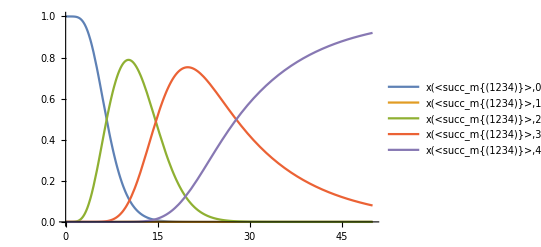

```mathematica
Block[{ix,fl,vl},
ix=Position[variables,x[EMU[Metabolite["succ","Mitochondria",_],{{{1,2,3,4}}}],_]];
fl=Extract[sol,ix];
vl=Extract[variables,ix];
Plot[
Evaluate[Table[Tooltip[fl⟦i⟧[t],vl⟦i⟧],{i,Length[ix]}]],
{t,0,tFinal},PlotLegends->vl]]
```

### End point, compare with steady state solution

```mathematica
MetaboliteEMUs[atomMap]
```

{<ac_c{(12)}>,<ac_m{(12)}>,<accoa_c{(12)}>,<accoa_m{(12)}>,<acnt_m{(123456)}>,<akg_m{(12345)}>,<cit_c{(123456)}>,<cit_m{(123456)}>,<co2_c{(1)}>,<co2_m{(1)}>,<fum_m{(1234)}>,<gln-L_c{(12345)}>,<gln-L_m{(12345)}>,<glu-L_m{(12345)}>,<hco3_m{(1)}>,<icit_m{(123456)}>,<mal-L_m{(1234)}>,<oaa_c{(1234)}>,<oaa_m{(1234)}>,<pyr_c{(123)}>,<pyr_m{(123)}>,<succ_m{(1234)}>,<succoa_m{(1234)}>}

Discrepancy due to epsilon flux through “zero” reactions -- should remove these

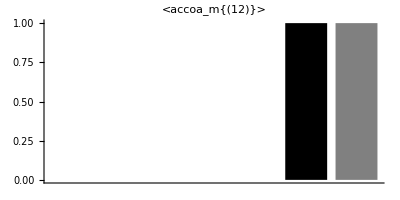
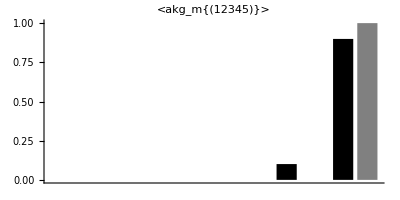
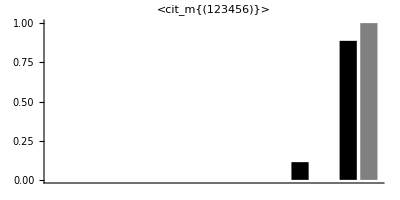
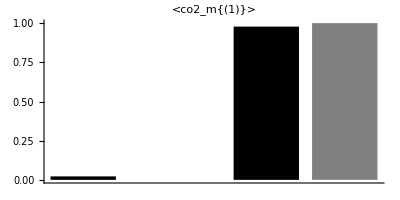
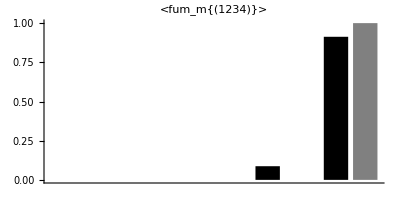
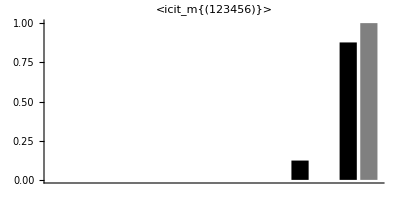
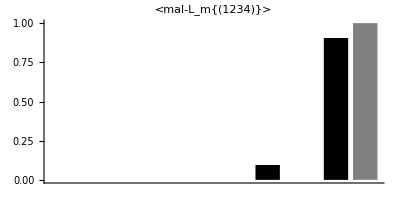
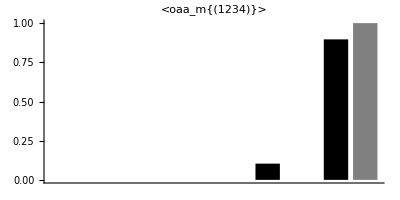

```mathematica
Block[{ix,fl},
Table[
ix=Position[variables,x[e,_]];
fl=Extract[sol,ix];
SimpleBarChart[
Transpose[{Evaluate[Table[f[tFinal],{f,fl}]],emuSol[e]}],
AspectRatio->1/2,PlotLabel->e],
{e,MetaboliteEMUs[atomMap]}]]
```

### Sample time points

```mathematica
timePoints={5,10,15,20,25};
```

```mathematica
samples=Block[{ix,functions},
Transpose[
Table[
ix=Position[variables,x[emu,_]];
functions=Extract[sol,ix];
Table[f[t],{t,timePoints},{f,functions}],
{emu,targets}]]];
```

```mathematica
Dimensions[samples]
```

{5,11}

Save as MI data set

```mathematica
fileName="C:\\Users\\rolnil\\OneDrive - KI.SE\\Lab common\\projects\\reverse-engineering-deniz\\reverse-engineering\\Data\\simulation\\tca_cycle\\tca-cycle-simple-model-nonstationary.tsv"
```

C:\Users\rolnil\OneDrive - KI.SE\Lab common\projects\reverse-engineering-deniz\reverse-engineering\Data\simulation\tca_cycle\tca-cycle-simple-model-nonstationary.tsv

```mathematica
Export[
fileName,
Block[{mi,met},
met=Flatten[Table[MetaboliteShortName[Metabolite[e]],{e,targets},{i,0,EMUSize[e]}]];
mi=Flatten[Table[Range[0,EMUSize[e]],{e,targets}]];
ArrayFlatten[
{{{{"Metabolite","MI"}},{timePoints}},
{Transpose[{met,mi}],Transpose[Flatten/@samples]}}]]
]
```

C:\Users\rolnil\OneDrive - KI.SE\Lab common\projects\reverse-engineering-deniz\reverse-engineering\Data\simulation\tca_cycle\tca-cycle-simple-model-nonstationary.tsv